## Config

```mathematica
(* Provide the location of the randgeom executable *)
(* On windows change randgeom to randgeom.exe *)
programlocation = "/home/mgv29/Desktop/randgeom"
```

/home/mgv29/Desktop/randgeom

```mathematica
(* Test the program. If it return False, check the programlocation provided. If it still does not work, first test randgeom from the console. *)
FileExistsQ[programlocation]&&ListQ[RunThrough["'"<>programlocation<>"'",""]]
```

True

## Useful functions

```mathematica
(* the following just runs randgeom with the specified parameters and parses the output as Mathematica code *)
generateMaps[type_,size_,number_]:=RunThrough["'"<>programlocation<>"' -t"<>type<>" -s"<>ToString[size]<>" -n"<>ToString[number], ""];
generateMap[type_,size_]:=First@generateMaps[type,size,1];
```

```mathematica
(* given a permutation p of {1,2,...,n}, cycles[p] gives the partition of {1,2,...,n} into cycles *)
cycles[p_]:=PermutationCycles[p,Identity];
(* given a list plist of permutations, orbits[plist] gives the partition of {1,2,...,n} into orbits under the permutations *)
orbits[plist_]:=GroupOrbits@PermutationGroup[PermutationCycles/@plist]
```

```mathematica
(* edges, vertices and faces correspond to cycles of halfedge-permutations *)
edgecycles[map_]:=cycles[map[[All,3]]];
facecycles[map_]:=cycles[map[[All,1]]];
vertexcycles[map_]:=cycles[map[[map[[All,3]],1]]];
(* We may assign id's to the vertices of map according to their position in vertexcycles[map] *)
halfedgeToVertexId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,vertexcycles[map],{2}]];
halfedgeToFaceId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,facecycles[map],{2}]];
```

```mathematica
(* functions to construct a Mathematica Graph object *)
uniqueEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToVertexId[map])];
uniqueDualEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToFaceId[map])];
mapGraph[map_]:=With[{edges=uniqueEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
mapDualGraph[map_]:=With[{edges=uniqueDualEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
```

## Plotting

```mathematica
(* the following is a bit of a hack to extract coordinates from GraphPlot3D's embedding of a graph *)
get3DGraphEmbedding[edg_,method_]:=(VertexCoordinateRules /. Cases[GraphPlot3D[#[[1]]->#[[2]]&/@edg,Method->method], _Rule, Infinity])[[Ordering@DeleteDuplicates[Join@@(List@@@edg)]]];
```

```mathematica
(* one can play with the options here to adapt the embedding *)
coordinates[map_]:=get3DGraphEmbedding[uniqueEdges[map],{"SpringElectricalEmbedding","InferentialDistance"->Automatic,"RepulsiveForcePower"->-2.4}];
```

```mathematica
(* assign colors to faces according to closeness centrality *)
colorFunction[x_]:=ColorData["Rainbow"][Round[Max[Min[0.55-0.15x,1],0],1/40]];
centralityColors[map_]:=colorFunction/@Standardize@ClosenessCentrality[mapDualGraph[map]];
```

```mathematica
plotMap3D[map_,coor_]:=Graphics3D[{EdgeForm[None],{FaceForm[#[[1]]],Polygon[coor[[#[[2,;;3]]]]],If[Length[#[[2]]]==4,Polygon[coor[[#[[2,{1,3,4}]]]]],{}]}&/@Transpose[{centralityColors[map],facecycles[map]/.halfedgeToVertexId[map]}]},Boxed->False]
```

```mathematica
map=generateMap["C",500];
plotMap3D[map,coordinates[map]]
```

Part::partd: Part specification VertexCoordinateRules⟦{1,2,4,3,5,26,12,31,13,14,«492»}⟧ is longer than depth of object.

Part::partw: Part {1,2,3} of VertexCoordinateRules⟦{1,2,4,3,5,26,12,31,13,14,«492»}⟧ does not exist.

Part::partw: Part {1,3,4} of VertexCoordinateRules⟦{1,2,4,3,5,26,12,31,13,14,«492»}⟧ does not exist.

Part::partw: Part {2,1,4} of VertexCoordinateRules⟦{1,2,4,3,5,26,12,31,13,14,«492»}⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* Task: plot geometries of various sizes and models. What are the qualitative differences between the models? *)
```

```mathematica
(* Task: produce some nice pictures. To save a nice picture, one may use something like Export["picture.png",ImageCrop@Rasterize[plot,ImageSize->800,Background->None]] *)
```

## Geodesic two-point function

```mathematica
(* Mathematica has built in support for graph distances: this returns a list of distances from all vertices to a randomly chosen vertex *)
distanceListFromRandomPoint[graph_]:=GraphDistance[graph,RandomChoice@VertexList[graph]];
```

```mathematica
(* produce a histogram with the fraction of points at distance 0,1,2,3,... *)
distanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapGraph[map];
dualDistanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapDualGraph[map];
```

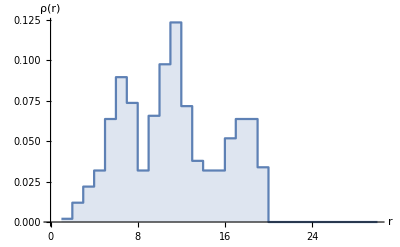

```mathematica
(* An example of a distance profile (from a random vertex) for a single random geometry *)
ListPlot[distanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

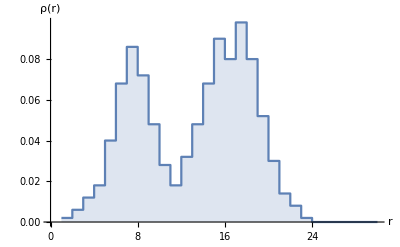

```mathematica
(* the same but for dual graph distance *)
ListPlot[dualDistanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

```mathematica
(* Task: Proceed to gather data for the average distance profile for different system sizes and models, and attempt finite-size scaling to extract the Hausdorff dimension *)
```

```mathematica
plotProfile[N_, B_] := ListPlot[distanceProfile[generateMap["C", N],B],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

ListPlot::lpn: 100[100[{1/102,1/102,11/102,5/17,11/34,7/102,1/17,4/51,5/102,0},16]] is not a list of numbers or pairs of numbers.

General::prng: Value of option PlotRange -> {{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},100[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1},{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},100[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partw: Part 2 of 100[{{-1.11111,1.11111},{-1.04167,1.04167}}] does not exist.

ListPlot::lpn: 10[10[{1/12,1/6,1/4,1/3,1/6,0,0,0,0,0},16]] is not a list of numbers or pairs of numbers.

General::prng: Value of option PlotRange -> {{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},10[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1},{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},10[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

MapThread::mptd: Object 10[{{-1.11111,1.11111},{-1.04167,1.04167}}] at position {2, 3} in MapThread[Visualization`Utilities`computeScaledGridLines[#1,#2,#3,#4]&,{{{Identity,Identity},{Identity,Identity}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,None}}] has only 0 of required 1 dimensions.

Part::partw: Part 2 of 10[{{-1.11111,1.11111},{-1.04167,1.04167}}] does not exist.

MapThread::mptd: Object MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[If[SameQ[«2»],Slot[«1»][«1»],Part[«3»]]]},Which[NumericQ[#1],#1,MatchQ[#2,Bottom|Left]||MatchQ[#4,Bottom|Left],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],MatchQ[#2,Top|Right]||MatchQ[#4,Top|Right],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][#3⟦2⟧],NumericQ[#4]&&Slot[«1»]⟦1⟧≤#4≤Slot[«1»]⟦2⟧,#4,NumericQ[#4]&&Slot[«1»]⟦1⟧>#4,Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}] at position {2, 3} in MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[«1»]},Which[NumericQ[Slot[«1»]],#1,MatchQ[«2»]||MatchQ[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][Part[«2»]],MatchQ[«2»]||MatchQ[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][Part[«2»]],NumericQ[«1»]&&LessEqual[«3»],#4,NumericQ[«1»]&&Greater[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][Part[«2»]],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object 10[{{-1.11111,1.11111},{-1.04167,1.04167}}] at position {2, 3} in MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[If[SameQ[«2»],Slot[«1»][«1»],Part[«3»]]]},Which[NumericQ[#1],#1,MatchQ[#2,Bottom|Left]||MatchQ[#4,Bottom|Left],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],MatchQ[#2,Top|Right]||MatchQ[#4,Top|Right],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][#3⟦2⟧],NumericQ[#4]&&Slot[«1»]⟦1⟧≤#4≤Slot[«1»]⟦2⟧,#4,NumericQ[#4]&&Slot[«1»]⟦1⟧>#4,Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}] has only 0 of required 1 dimensions.

ListPlot::lpn: 100[100[{1/102,1/102,2/17,9/34,31/102,1/6,4/51,2/51,1/102,0},16]] is not a list of numbers or pairs of numbers.

General::prng: Value of option PlotRange -> {{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},100[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1},{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},100[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partw: Part 2 of 100[{{-1.11111,1.11111},{-1.04167,1.04167}}] does not exist.

ListPlot::lpn: 10[10[{1/12,5/12,1/4,1/6,1/12,0,0,0,0,0},16]] is not a list of numbers or pairs of numbers.

General::prng: Value of option PlotRange -> {{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},10[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1},{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},10[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

MapThread::mptd: Object 10[{{-1.11111,1.11111},{-1.04167,1.04167}}] at position {2, 3} in MapThread[Visualization`Utilities`computeScaledGridLines[#1,#2,#3,#4]&,{{{Identity,Identity},{Identity,Identity}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,None}}] has only 0 of required 1 dimensions.

Part::partw: Part 2 of 10[{{-1.11111,1.11111},{-1.04167,1.04167}}] does not exist.

MapThread::mptd: Object MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[If[SameQ[«2»],Slot[«1»][«1»],Part[«3»]]]},Which[NumericQ[#1],#1,MatchQ[#2,Bottom|Left]||MatchQ[#4,Bottom|Left],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],MatchQ[#2,Top|Right]||MatchQ[#4,Top|Right],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][#3⟦2⟧],NumericQ[#4]&&Slot[«1»]⟦1⟧≤#4≤Slot[«1»]⟦2⟧,#4,NumericQ[#4]&&Slot[«1»]⟦1⟧>#4,Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}] at position {2, 3} in MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[«1»]},Which[NumericQ[Slot[«1»]],#1,MatchQ[«2»]||MatchQ[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][Part[«2»]],MatchQ[«2»]||MatchQ[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][Part[«2»]],NumericQ[«1»]&&LessEqual[«3»],#4,NumericQ[«1»]&&Greater[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][Part[«2»]],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object 10[{{-1.11111,1.11111},{-1.04167,1.04167}}] at position {2, 3} in MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[If[SameQ[«2»],Slot[«1»][«1»],Part[«3»]]]},Which[NumericQ[#1],#1,MatchQ[#2,Bottom|Left]||MatchQ[#4,Bottom|Left],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],MatchQ[#2,Top|Right]||MatchQ[#4,Top|Right],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][#3⟦2⟧],NumericQ[#4]&&Slot[«1»]⟦1⟧≤#4≤Slot[«1»]⟦2⟧,#4,NumericQ[#4]&&Slot[«1»]⟦1⟧>#4,Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},10[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object 100[{{-1.11111,1.11111},{-1.04167,1.04167}}] at position {2, 3} in MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[If[SameQ[«2»],Slot[«1»][«1»],Part[«3»]]]},Which[NumericQ[#1],#1,MatchQ[#2,Bottom|Left]||MatchQ[#4,Bottom|Left],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],MatchQ[#2,Top|Right]||MatchQ[#4,Top|Right],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][#3⟦2⟧],NumericQ[#4]&&Slot[«1»]⟦1⟧≤#4≤Slot[«1»]⟦2⟧,#4,NumericQ[#4]&&Slot[«1»]⟦1⟧>#4,Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},100[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[If[SameQ[«2»],Slot[«1»][«1»],Part[«3»]]]},Which[NumericQ[#1],#1,MatchQ[#2,Bottom|Left]||MatchQ[#4,Bottom|Left],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],MatchQ[#2,Top|Right]||MatchQ[#4,Top|Right],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][#3⟦2⟧],NumericQ[#4]&&Slot[«1»]⟦1⟧≤#4≤Slot[«1»]⟦2⟧,#4,NumericQ[#4]&&Slot[«1»]⟦1⟧>#4,Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][#3⟦1⟧],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},100[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}] at position {2, 3} in MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{Visualization`Utilities`OptionsDump`checkpoint=Quiet[«1»]},Which[NumericQ[Slot[«1»]],#1,MatchQ[«2»]||MatchQ[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][Part[«2»]],MatchQ[«2»]||MatchQ[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Smaller][Part[«2»]],NumericQ[«1»]&&LessEqual[«3»],#4,NumericQ[«1»]&&Greater[«2»],Visualization`Utilities`OptionsDump`nudgeAxesOrigin[Larger][Part[«2»]],«10»]]&,{{{-1,1},{-1,1}},{Automatic,Automatic},100[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,Automatic},{1,2},{Identity,Identity}}]}] has only 0 of required 1 dimensions.

Part::partw: Part 2 of 100[{{-1.11111,1.11111},{-1.04167,1.04167}}] does not exist.

MapThread::mptd: Object 100[{{-1.11111,1.11111},{-1.04167,1.04167}}] at position {2, 3} in MapThread[Visualization`Utilities`computeScaledGridLines[#1,#2,#3,#4]&,{{{Identity,Identity},{Identity,Identity}},{Automatic,Automatic},100[{{-1.11111,1.11111},{-1.04167,1.04167}}],{None,None}}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},100[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1},{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},100[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: 100[100[{1/102,1/34,5/51,4/17,23/102,7/51,1/17,7/51,7/102,0,«20»},16]] is not a list of numbers or pairs of numbers.

Part::partw: Part 2 of 200[{{-1.11111,1.11111},{-1.04167,1.04167}}] does not exist.

General::prng: Value of option PlotRange -> {{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},200[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1},{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},200[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: 200[200[{1/202,1/202,3/202,7/101,9/101,10/101,21/202,41/202,22/101,14/101,«20»},16]] is not a list of numbers or pairs of numbers.

Part::partw: Part 2 of 500[{{-1.11111,1.11111},{-1.04167,1.04167}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},500[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1},{MapThread[If[NumericQ[#1],#2,Min[#2,#3]]&,{{Automatic,Automatic},{-1,-1},MapThread[With[{«1»},Which[«20»]]&,{{{«2»},{«2»}},{Automatic,Automatic},500[{«2»}],{None,Automatic},{1,2},{Identity,Identity}}]}],1}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

ListPlot::lpn: 500[500[{1/502,1/251,4/251,13/251,43/502,63/502,107/502,52/251,89/502,21/251,«20»},16]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

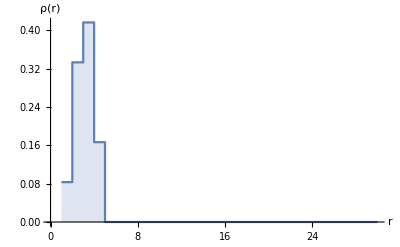

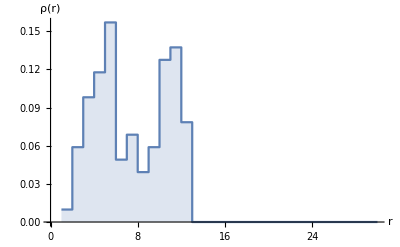

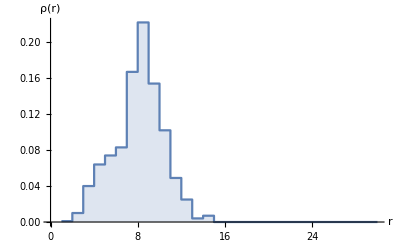

```mathematica
plotProfile[10, 30]
plotProfile[100, 30]
plotProfile[1000, 30]
```

## Spectral dimension

The spectral dimension d_s of a map is related to the probability p(t) that a simple random walk on the map (or its dual) returns to its starting point after t steps: p(t) ~ t^(-d_s/2) for 1<< t << n (where n is the system size). There are various ways to measure this return probability: one can simulate a random walker and just record its returns; study a heat diffusion process; or use linear algebra as follows. The return probability ⟨p(t)⟩ averaged over all starting points of the map is related to the normalized adjacency matrix A via  ⟨p(t)⟩=Tr(A^t)/n = ∑λ_i^t/n, where λ_i are the eigenvalues of A.

```mathematica
dualAdjacencyMatrix[map_]:=Module[{dualedges,matrixentries,facedegrees},
dualedges=edgecycles[map]/.halfedgeToFaceId[map];
facedegrees=Length/@facecycles[map];
matrixentries =Tally@Join[dualedges,Reverse/@dualedges];
SparseArray[#[[1]]->#[[2]]/facedegrees[[#[[1,1]]]]&/@matrixentries]
]
```

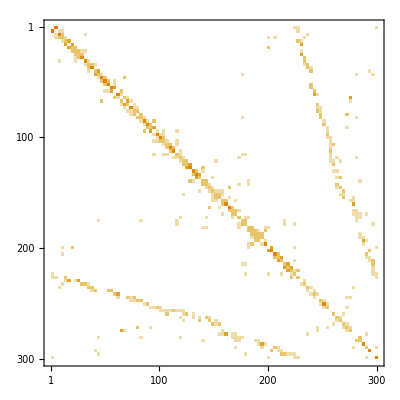

```mathematica
(* plot the adjacency matrix (for fun) *) 
MatrixPlot[dualAdjacencyMatrix[generateMap["D",300]]]
```

```mathematica
dualAdjacencySpectrum[map_]:=Sort@Eigenvalues@Normal@N@dualAdjacencyMatrix[map]
```

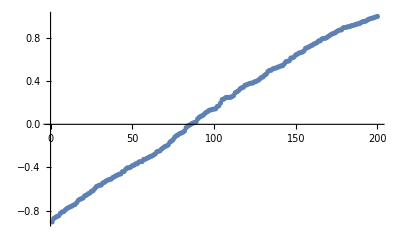

```mathematica
(* a plot of the spectrum of a random geometry *)
ListPlot[dualAdjacencySpectrum[generateMap["A",200]]]
```

```mathematica
(* The return probability of a random walker after k steps averaged over all starting points. *)
(* Notice one can may take range to be e.g. 2^Range[14] to get the return probability for {t=2,t=4,...,t=2^14} without problem. *)
returnProbability[map_,range_]:=With[{spec=dualAdjacencySpectrum[map]},Table[{t,Mean[spec^t]},{t,range}]]
```

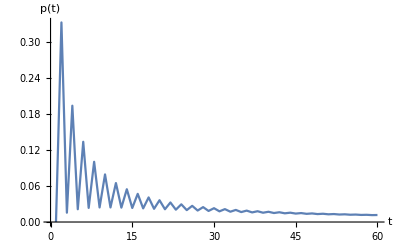

```mathematica
(* A plot of the return probability for a single random geometry *)
(* Notice the alternating pattern. Do you understand why it occurs? *)
ListPlot[returnProbability[generateMap["D",500],Range[60]],Joined->True,AxesLabel->{"t","p(t)"},PlotRange->All]
```

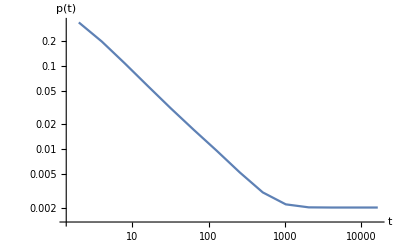

```mathematica
(* A logarithmic plot of the return probability for a single random geometry at large time, showing the finite size effects *)
(* The return probability approaches a constant at late times. What value does it take? *)
ListLogLogPlot[returnProbability[generateMap["A",500],2^Range[14]],Joined->True,AxesLabel->{"t","p(t)"}]
```

```mathematica
(* Task: Gather data for various system sizes and models and try to extract the spectral dimension by fitting the slope (in the logarithmic plot) *)
```

```mathematica
alldata = Log[returnProbability[generateMap["D",500],2^Range[14]]]
data = alldata[[2;; 8]]
fit = LinearModelFit[data, {1, x}, {x}]
{a, b} = fit["BestFitParameters"]
```

{{Log[2],-1.09861},{Log[4],-1.63748},{Log[8],-2.28902},{Log[16],-3.02732},{Log[32],-3.78583},{Log[64],-4.48132},{Log[128],-5.10574},{Log[256],-5.66761},{Log[512],-6.06767},{Log[1024],-6.203},{Log[2048],-6.21451},{Log[4096],-6.21461},{Log[8192],-6.21461},{Log[16384],-6.21461}}

{{Log[4],-1.63748},{Log[8],-2.28902},{Log[16],-3.02732},{Log[32],-3.78583},{Log[64],-4.48132},{Log[128],-5.10574},{Log[256],-5.66761}}

FittedModel[-0.288863-0.988134 x]

{-0.288863,-0.988134}

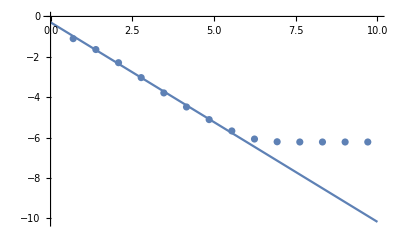

```mathematica
Show[{Plot[fit[x],{x,0,10}],ListPlot[alldata]}]
```

Spectral dimension is: d_s == -2 b  2

## Susceptibility exponent / counting exponent

Another important exponent is the susceptibility exponent γ (also known as the counting exponent) which governs the growth of the (unlabeled) partition function with increasing system size:  Z(n)~n^(γ-3)ⅇ^(-c n) (assuming we have no marking/root). One way to determine this exponent is to look for minimal necks in the map, i.e. closed paths of minimal length on the map (which for our purposes is typically length 2). For each minimal neck one may determine the distribution of the number m of faces/edges/vertices it encloses. This distribution should for large n,m be proportional to (m(n-m))^(γ-2), and fitting the data provides an estimate for γ. Be aware that for this measurement to work one needs an abundance of minimal necks, which is not necessarily the case for all models.

```mathematica
(* Below is a crude way to identify minimal necks. Do you know of a better way? *)
```

```mathematica
(* find pairs of vertices with more than one connecting edge *)
vertexPairsWithDoubleEdges[map_]:=Select[Normal@GroupBy[edgecycles[map]//Transpose[{#,#/.halfedgeToVertexId[map]}]&,Sort@Last@#&],Length[#[[2]]]>1&][[All,1]];
```

```mathematica
(* a brute force way to determine the (smallest of the two) enclosed volumes: remove the pair of vertices from the graph, and determine the sizes of the remaining connected components *)
componentSize[graph_,vertexpair_]:=Min[#,VertexCount[graph]-#]&@Length@RandomChoice@WeaklyConnectedComponents@VertexDelete[graph,vertexpair]
```

```mathematica
(* an example of the number of vertices in all the regions enclosed by minimal necks in a single random geometry *)
map=generateMap["C",200];
graph=mapGraph[map];
componentSize[mapGraph[map],#]&/@vertexPairsWithDoubleEdges[map]
```

{4,1,1,5,1,1,1,3,24,23,2,1,4,6,6,1,3,1,1,1,3,3,1,3,5,1,9,8,12,4,1,1,1,1,7,1,1,3,1,3,4,1,1,1,2,3,1,1,1,1,2,4,48,1,7,4,1,12,1,9,1,3,1,4,7,2,1,1,14,1,1,1,2,1,1,4,6,5,2,1}

```mathematica
(* Task: Produce histograms for the volume enclosed by minimal necks in random geometries of various sizes and models; make a logarithmic plot of the histogram (normalized by 1/V where V is the number of vertices of the geometry) against n(1-n/V) and extract γ from the slope of the curve. *)
```